```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA_CT",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs}];
```

## t- t (1-loop - self energy)

```mathematica
tops = CreateTopologies[1,1->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
topsCT = CreateCTTopologies[1,1->1,ExcludeTopologies->{WFCorrectionCTs,TadpoleCTs,BoxCTs,TriangleCTs}]
processGGT =  { F[9]}-> {F[9]};
allDiags = InsertFields[Join[tops,topsCT],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8],V[4]}];
```

TopologyList(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(2,1)(3)),Propagator(Outgoing)(Vertex(1)(2),Vertex(2,1)(3))))

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA_CT} initialized

in total: 2 Particles insertions

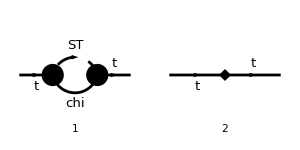

```mathematica
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p},LorentzIndexNames->{μ,ν},OutgoingMomenta->{p},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
```

in total: 2 Particles amplitudes

```mathematica
ampC =( TID[ampA,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]);
```

```mathematica
ampC
```

(ⅈ π^2 yDM^2 δ_Col1Col2 (-MT (γ·p).(γ̄)^6 (-((mChi^2-mST^2+p^2) B_0(p^2,mChi^2,mST^2))/(2 p^2)+(A_0(mChi^2))/(2 p^2)-(A_0(mST^2))/(2 p^2))+deltaS (γ·p).(γ̄)^7+deltaSp MT (γ·p).(γ̄)^6+deltaS MT))/MT

```mathematica
Collect[PowerExpand[PaXEvaluate[ampC,PaXImplicitPrefactor->1/(2 Pi)^(4- 2 Epsilon)]/.{EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))}],{Epsilon,Log[ScaleMu],deltaSp},Simplify]
```

1/(64 π^2)ⅈ yDM^2 δ_Col1Col2 ((4 deltaS (γ·p).(γ̄)^7)/MT-(2 (mChi-mST) (mChi+mST) √(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4) (γ·p).(γ̄)^6 (-log(√(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4)+mChi^2+mST^2-p^2)+log(mChi)+log(mST)+log(2)))/p^4-(2 √(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4) (γ·p).(γ̄)^6 (-log(√(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4)+mChi^2+mST^2-p^2)+log(mChi)+log(mST)+log(2)))/p^2+(2 (mChi^2+2 mST^2 log(mChi)-mST^2-2 mST^2 log(mST)) (γ·p).(γ̄)^6)/p^2-(2 (mChi-mST)^2 (mChi+mST)^2 log(mChi/mST) (γ·p).(γ̄)^6)/p^4-2 log(mChi mST) (γ·p).(γ̄)^6+4 (γ·p).(γ̄)^6+4 log(2 π) (γ·p).(γ̄)^6-4 log(π) (γ·p).(γ̄)^6-4 log(2) (γ·p).(γ̄)^6+4 deltaS)+(ⅈ deltaSp yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(16 π^2)+(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(32 π^2 ε)+(ⅈ yDM^2 log(μ) δ_Col1Col2 (γ·p).(γ̄)^6)/(16 π^2)

```mathematica
$Assumptions={MT>0,mST>0,mChi>0,mST>mChi+MT};
```

```mathematica
deltaSval=Simplify[(-mST/(32*Pi^4*xT^(3/2)))*(xT*(2*xC+xT-2)+(-xC^2+2*xC+xT-1)*Log[xC]-2*(-xC^3+(3+xT)*xC^2+(xT-3)*xC+(xT-1)^2)*Log[(xC-xT+Sqrt[lA]+1)/(2*Sqrt[xC])]/(Sqrt[lA]))//.{xC-> mChi^2/mST^2,xT->MT^2/mST^2,lA->1+xC^2+xT^2-2*xC-2*xT-2*xT*xC}];
deltaSpval=Simplify[(1/(64*Pi^4*xT^2))*(2*xT*(xC-xT-1)+(-xC^2+2*xC+xT^2-1)*Log[xC]+2*(xC^3-(3+xT)*xC^2+(xT^2+3)*xC-(xT+1)*(xT-1)^2)*Log[(xC-xT+Sqrt[lA]+1)/(2*Sqrt[xC])]/(Sqrt[lA]))//.{xC-> mChi^2/mST^2,xT->MT^2/mST^2,lA->1+xC^2+xT^2-2*xC-2*xT-2*xT*xC}];
logVal=-1/(32 Pi^4)Log[μ^2/mST^2];
```

```mathematica
mChiv=100.;
yDMv=1.;
mSTv=400.;
MTv=172.;
gsv=√1.6336281798666927;
muv=91.188000;
vals={mChi->mChiv,mST->mSTv,MT->MTv,yDM->yDMv,gs->gsv,μ-> muv};
```

```mathematica
((I Pi^2  yDM^2)deltaSval)/.vals
((I Pi^2  yDM^2)deltaSval/MT)/.vals
```

0.+0.0331582 ⅈ

0.+0.00019278 ⅈ

```mathematica
UVGC13176=0.33158 10^(-01) *I
UVGC12972= 0.19278 10^(-3)*I
```

0.+0.033158 ⅈ

0.+0.00019278 ⅈ

```mathematica
((I Pi^2  yDM^2)deltaSpval)/.vals
((I Pi^2  yDM^2)(deltaSpval+logVal))/.vals
```

0.-0.0017887 ⅈ

0.+0.00757428 ⅈ

```mathematica
UVGC13278=-0.75743 10^(-2) *I
```

0.-0.0075743 ⅈ

```mathematica
logVal/.vals
```